## Конечные цепи Маркова: задача о благосостоянии

### Даны вероятности перехода из класса в класс для домохозяйств:

Зададим матрицу вероятностей перехода

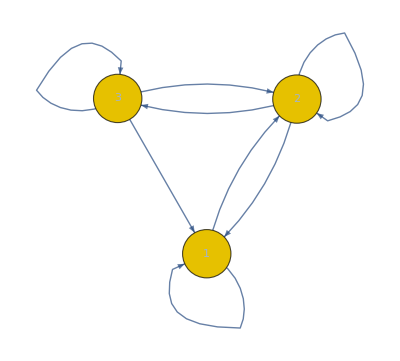
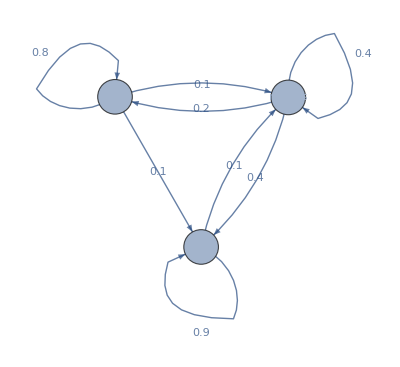
(0.9 | 0.1 | 0
0.4 | 0.4 | 0.2
0.1 | 0.1 | 0.8) | -Graphics- | -Graphics-

CommunicatingClasses | {{1,2,3}}
RecurrentClasses | {{1,2,3}}
TransientClasses | {}
AbsorbingClasses | {}
PeriodicClasses | {}
Periods | {}
Irreducible | True
Aperiodic | True
Primitive | True

```mathematica
Clear["Global`*"]
P={{0.9,0.1,0},{0.4,0.4,0.2},{0.1,0.1,0.8}};
proc=DiscreteMarkovProcess[1,P];
Grid[{{
P//MatrixForm,
Graph[proc],
WeightedAdjacencyGraph[
P/. 0|0.->Infinity,
VertexShapeFunction->"Circle",
VertexSize->0.2,
EdgeLabels->"EdgeWeight",
VertexLabels->(       #[[1]]-> Placed[#[[2]],Center]&/@Transpose[{Range[3],{"poor","mclass","rich"}}]     )
]
}}]

Grid[{
{"CommunicatingClasses",MarkovProcessProperties[proc,"CommunicatingClasses"]},(*неразложимая цепь Маркова*)
{"RecurrentClasses",MarkovProcessProperties[proc,"RecurrentClasses"]},(*возвратная цепь Маркова*)
{"TransientClasses",MarkovProcessProperties[proc,"TransientClasses"]},(*невозвратная цепь Маркова*)
{"AbsorbingClasses",MarkovProcessProperties[proc,"AbsorbingClasses"]},(*поглощающее состояние*)
{"PeriodicClasses",MarkovProcessProperties[proc,"PeriodicClasses"]},(*периодическая/циклическая цепь Маркова*)
{"Periods",MarkovProcessProperties[proc,"Periods"]},(*переодическая*)
{"Irreducible",MarkovProcessProperties[proc,"Irreducible"]},(*неприводимая/неразложимая цепь Маркова*)
{"Aperiodic",MarkovProcessProperties[proc,"Aperiodic"]},(*непереодическая*)
{"Primitive",MarkovProcessProperties[proc,"Primitive"]}(*простой цепью Маркова*)
}]
```

Матрица времени среднего перехода из каждого состояния

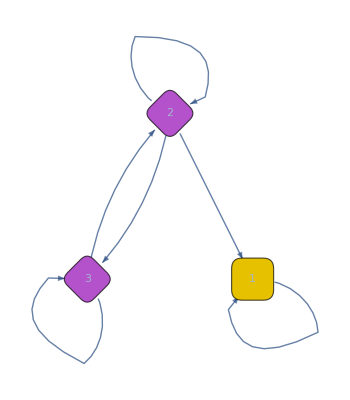
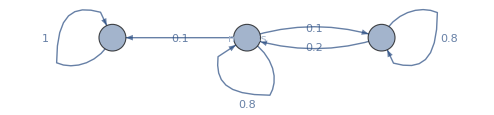
(1 | 0 | 0
0.1 | 0.8 | 0.1
0 | 0.2 | 0.8) | -Graphics- | -Graphics-

CommunicatingClasses | {{1},{2,3}}
RecurrentClasses | {{1}}
TransientClasses | {{2,3}}
AbsorbingClasses | {{1}}
PeriodicClasses | {}
Periods | {}
Irreducible | False
Aperiodic | True
Primitive | False

```mathematica
Clear["Global`*"]
P={{1,0,0},{0.1,0.8,0.1},{0,0.2,0.8}};
proc=DiscreteMarkovProcess[1,P];
Grid[{{
P//MatrixForm,
Graph[proc],
WeightedAdjacencyGraph[
P/. 0|0.->Infinity,
VertexShapeFunction->"Circle",
VertexSize->0.2,
EdgeLabels->"EdgeWeight",
VertexLabels->(       #[[1]]-> Placed[#[[2]],Center]&/@Transpose[{Range[3],{"poor","mclass","rich"}}]     )
]
}}]

Grid[{
{"CommunicatingClasses",MarkovProcessProperties[proc,"CommunicatingClasses"]},
{"RecurrentClasses",MarkovProcessProperties[proc,"RecurrentClasses"]},
{"TransientClasses",MarkovProcessProperties[proc,"TransientClasses"]},
{"AbsorbingClasses",MarkovProcessProperties[proc,"AbsorbingClasses"]},
{"PeriodicClasses",MarkovProcessProperties[proc,"PeriodicClasses"]},
{"Periods",MarkovProcessProperties[proc,"Periods"]},
{"Irreducible",MarkovProcessProperties[proc,"Irreducible"]},
{"Aperiodic",MarkovProcessProperties[proc,"Aperiodic"]},
{"Primitive",MarkovProcessProperties[proc,"Primitive"]}
}]
```

Матрица времени среднего перехода из каждого состояния

{{0.,1.,0.,0.},{0.5,0.,0.5,0.},{0.,0.5,0.,0.5},{0.,0.,1.,0.}}

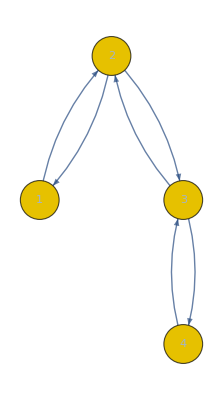
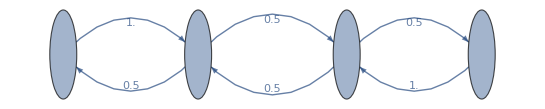
(0. | 1. | 0. | 0.
0.5 | 0. | 0.5 | 0.
0. | 0.5 | 0. | 0.5
0. | 0. | 1. | 0.) | -Graphics- | -Graphics-

CommunicatingClasses | {{1,2,3,4}}
RecurrentClasses | {{1,2,3,4}}
TransientClasses | {}
AbsorbingClasses | {}
PeriodicClasses | {{1,2,3,4}}
Periods | {2}
Irreducible | True
Aperiodic | False
Primitive | False

```mathematica
P={{0.0,1.0,0.0,0.0},{0.5,0.0,0.5,0.0},{0.0,0.5,0.0,0.5},{0.0,0.0,1.0,0.0}}
proc=DiscreteMarkovProcess[1,P];
Grid[{{
P//MatrixForm,
Graph[proc],
WeightedAdjacencyGraph[
P/. 0.->Infinity,
VertexShapeFunction->"Circle",
VertexSize->0.2,
EdgeLabels->"EdgeWeight",
VertexLabels->(       #[[1]]-> Placed[#[[2]],Center]&/@Transpose[{Range[4],{"a","b","c","d"}}]     )
]
}}]

Grid[{
{"CommunicatingClasses",MarkovProcessProperties[proc,"CommunicatingClasses"]},
{"RecurrentClasses",MarkovProcessProperties[proc,"RecurrentClasses"]},
{"TransientClasses",MarkovProcessProperties[proc,"TransientClasses"]},
{"AbsorbingClasses",MarkovProcessProperties[proc,"AbsorbingClasses"]},
{"PeriodicClasses",MarkovProcessProperties[proc,"PeriodicClasses"]},
{"Periods",MarkovProcessProperties[proc,"Periods"]},
{"Irreducible",MarkovProcessProperties[proc,"Irreducible"]},
{"Aperiodic",MarkovProcessProperties[proc,"Aperiodic"]},
{"Primitive",MarkovProcessProperties[proc,"Primitive"]}
}]
```